## Numerical Example Ambartsumyan et al. CMAME (2020) :

```mathematica
lambda->1
mu->1
alpha->1
c0->1e-05
K->perm*eye(2)
```

### Displacement :

```mathematica
u[x_,y_]:={x,0}
```

Dirichlet boundary conditions : (they are not homogeneous)

```mathematica
u[0,y]
```

{0,0}

```mathematica
u[1,y]
```

{1,0}

```mathematica
u[x,0]
```

{x,0}

```mathematica
u[x,1]
```

{x,0}

ContourPlot of the Magnitude of the displacement (Euclidean norm) :

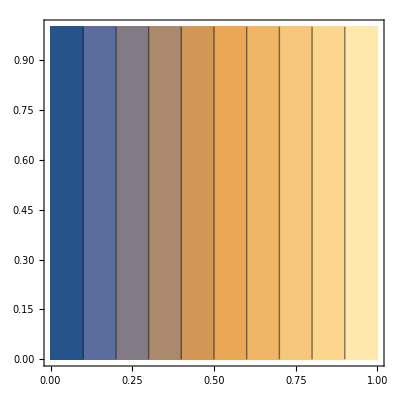

```mathematica
ContourPlot[Sqrt[(x)^2+(0)^2],{x,0,1},{y,0,1}]
```

### Pressure:

```mathematica
p[x_,t_]:= x
```

```mathematica
ContourPlot[p[x,0.001],{x,0,1},{y,0,1}]
```

-Graphics-

### Elastic Stress:

```mathematica
{D[(x), x],D[(x), y]}//Simplify
```

{1,0}

```mathematica
{D[(0), x],D[(0), y]}//Simplify
```

{0,0}

```mathematica
Gradu:={{1,0},{0,0}}
```

Let us define ϵ (u) :

```mathematica
1/2*(Gradu+Transpose[Gradu])//Simplify
```

{{1,0},{0,0}}

Let us compute the stress σ= A^-1 ϵ(u): (Using the expression for A^-1 given in equation (3 . 2 . 9) of Ambartsumyan PhD. Thesis)

```mathematica
2 mu {{1,0},{0,0}}+lambda {{1,0},{0,1}}//Simplify
```

{{lambda+2 mu,0},{0,lambda}}

Let us define the stress function as the previous expression :

```mathematica
Sigmae:={{lambda+2 mu,0},{0,lambda}}
```

### Stress:

```mathematica
Sigmae-alpha {{p[x,t],0},{0,p[x,t]}}//Simplify
```

{{lambda+2 mu-alpha x,0},{0,lambda-alpha x}}

```mathematica
Sigma[x_,t_]:={{lambda+2 mu-alpha x,0},{0,lambda-alpha x}}
```

ContourPlot of the Magnitude of the first row of σ :

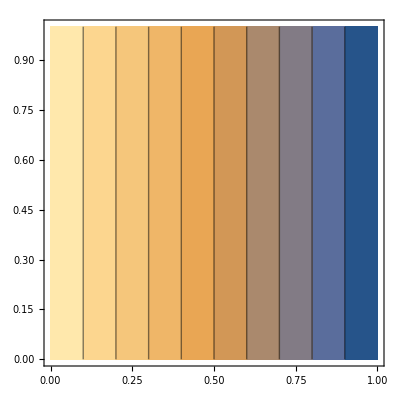

```mathematica
ContourPlot[Sqrt[(lambda+2 mu-alpha x)^2+(0)^2]/.{t->0.001,lambda ->1,mu->1,alpha->1},{x,0,1},{y,0,1}]
```

ContourPlot of the Magnitude of the second row of σ :

```mathematica
ContourPlot[Sqrt[(0)^2+(lambda-alpha x)^2]/.{t->0.001,lambda ->1,mu->1,alpha->1},{x,0,1},{y,0,1}]
```

-Graphics-

### Rotation :

```mathematica
1/2*(Gradu-Transpose[Gradu])//Simplify
```

{{0,0},{0,0}}

ContourPlot of the element in the first row and second column of the rotation:

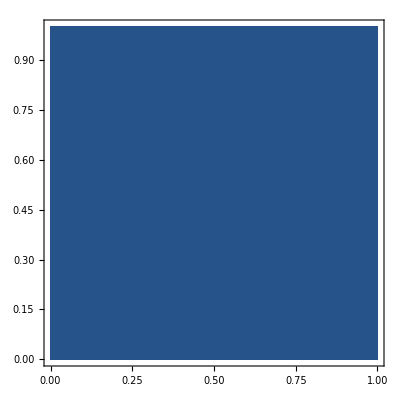

```mathematica
ContourPlot[0,{x,0,1},{y,0,1}]
```

### Darcy velocity :

```mathematica
KK:=perm*{{1, 0},{0, 1}}
```

```mathematica
-KK.{D[p[x,t],x],D[p[x,t],y]}//Simplify
```

{-perm,0}

```mathematica
z[t_]:={-perm ,0}
```

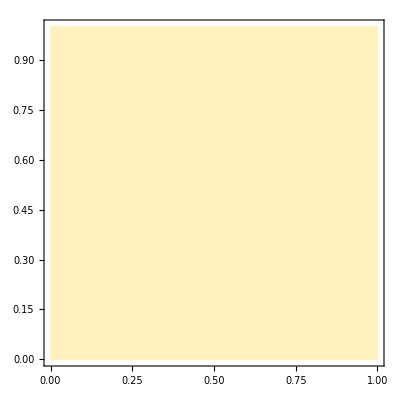

```mathematica
ContourPlot[Sqrt[(-perm )^2+(0)^2]/.{t->0.001, perm->1},{x,0,1},{y,0,1}]
```

### Source term f :

```mathematica
Sigma[x,t]
```

{{lambda+2 mu-alpha x,0},{0,lambda-alpha x}}

```mathematica
-(D[lambda+2 mu-alpha x,x]+D[0,y])//Simplify
```

alpha

```mathematica
f1[t_]:=alpha
```

```mathematica
-(D[0,x]+D[lambda-alpha x,y])//Simplify
```

0

```mathematica
f2:=0
```

### Source term q :

```mathematica
u[x,y]
```

{x,0}

```mathematica
z[t]
```

{-perm,0}

```mathematica
D[c0 p[x,t]+alpha (D[x,x]+D[0,y]),t]+D[-perm ,x]+D[0,y]//Simplify
```

0

```mathematica
FortranForm[0/.{x->xx}]
```

0